```mathematica
rawData = Partition[ReadList["C:/Unity/SyntheticGS/Assets/HDRI/Histogram.dat", "Number"], 100];
Manipulate[BarChart[rawData[[a]]], {a, 1, 10, 1}]
```

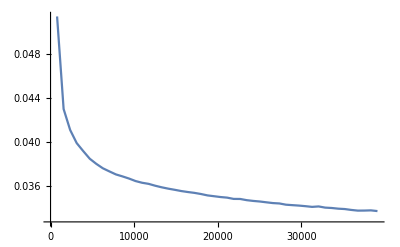

```mathematica
lossData = Partition[ReadList["C:/Unity/SyntheticGS/Assets/HDRI/Loss.dat", "Number"], 2];
ListLinePlot[lossData, PlotRange->All]
```

```mathematica
filePath = "C:/Unity/SyntheticGS/Assets/HDRI/Loss.dat";
miniBatchStr = ReadLine[filePath];
epochStr = ReadLine[filePath];
Close[filePath];
(*StringToStream[miniBatchStr]*)
(*epochLoss = Partition[ReadList[StringToStream[epochStr], "Number"], 2];
miniBatchLoss= Partition[ReadList[StringToStream[miniBatchStr], "Number"], 2];
ListLinePlot[{miniBatchLoss, epochLoss}, PlotRange->All]*)
```

Options::strmn: Requested stream InputStream[C:/Unity/SyntheticGS/Assets/HDRI/Loss.dat,64] does not match existing stream {System`Private`StringTurnedIntoStream[782 0.051443 1564 0.043031 2346 0.041129 3128 0.039936 3910 0.039209 4692 0.038514 5474 0.038049 6256 0.037648 7038 0.037363 782...44 0.034073 33626 0.034039 34408 0.033977 35190 0.033943 35972 0.033862 36754 0.033800 37536 0.033805 38318 0.033823 39100 0.033758 ],{False,String,False},-Medium-} with the same stream number.

```mathematica
filePath = "C:/Unity/SyntheticGS/Assets/HDRI/Loss.dat";
miniBatchStr = ReadLine[filePath];
epochStr = ReadLine[filePath];
Close[filePath];
StringToStream[miniBatchStr]
epochLoss = Partition[ReadList[StringToStream[epochStr], "Number"], 2];
miniBatchLoss= Partition[ReadList[StringToStream[miniBatchStr], "Number"], 2];
ListLinePlot[{miniBatchLoss, epochLoss}, PlotRange->{All, {0, 0.2}}]
```

Options::strmn: Requested stream InputStream[C:/Unity/SyntheticGS/Assets/HDRI/Loss.dat,48] does not match existing stream {System`Private`StringTurnedIntoStream[0 10.048344 1 4.844222 2 5.161750 3 3.287568 4 2.304590 5 1.807089 6 1.591855 7 1.902719 8 1.534210 9 1.182109 10 1.306495 11 1....91 0.035521 15692 0.033657 15693 0.027906 15694 0.032242 15695 0.027221 15696 0.014513 15697 0.033872 15698 0.019929 15699 0.019929 ],{False,String,False},-Medium-} with the same stream number.

InputStream[…]

StringToStream::string: String expected at position 1 in StringToStream[EndOfFile].

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ReadList::stream: ReadList[$Failed,Number] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

General::stop: Further output of ReadList::stream will be suppressed during this calculation.

ListLinePlot::lpn: {{{1.,0.887676},{2.,0.887576},{3.,0.887476},{4.,0.887376},{5.,0.887277},{6.,0.887177},{7.,0.887078},{8.,0.886978},{9.,0.886878},{10.,0.886779},{11.,0.886679},{12.,0.886579},{13.,0.88648},{14.,0.88638},{15.,0.886281},«22»,{38.,0.884387},{39.,0.88432},{40.,0.884252},{41.,0.884184},{42.,0.884117},{43.,0.884049},{44.,0.883982},{45.,0.883923},{46.,0.883827},{47.,0.883732},{48.,0.883637},{49.,0.883541},{50.,0.883446},«950»},{}} is not a list of numbers or pairs of numbers.

ListLinePlot[{{{1,0.887676},{2,0.887576},{3,0.887476},{4,0.887376},{5,0.887277},{6,0.887177},{7,0.887078},{8,0.886978},{9,0.886878},{10,0.886779},{11,0.886679},{12,0.886579},{13,0.88648},{14,0.88638},{15,0.886281},{16,0.886183},{17,0.886085},{18,0.885986},{19,0.885888},{20,0.885791},{21,0.885693},{22,0.885595},{23,0.885498},{24,0.885401},{25,0.885304},{26,0.885208},{27,0.885139},{28,0.88507},{29,0.885002},{30,0.884933},{31,0.884865},{32,0.884796},{33,0.884728},{34,0.88466},{35,0.884591},{36,0.884523},{37,0.884455},{38,0.884387},{39,0.88432},{40,0.884252},{41,0.884184},{42,0.884117},{43,0.884049},{44,0.883982},{45,0.883923},{46,0.883827},{47,0.883732},{48,0.883637},{49,0.883541},{50,0.883446},{51,0.883352},{52,0.883257},{53,0.883162},{54,0.883068},{55,0.882973},{56,0.882878},{57,0.882783},{58,0.882689},{59,0.882594},{60,0.8825},{61,0.882405},{62,0.882311},{63,0.882217},{64,0.882123},{65,0.882028},{66,0.881934},{67,0.881839},{68,0.881744},{69,0.88165},{70,0.881556},{71,0.881461},{72,0.881367},{73,0.881272},{74,0.881177},{75,0.881082},{76,0.880987},{77,0.880893},{78,0.880797},{79,0.880701},{80,0.880606},{81,0.880511},{82,0.880416},{83,0.880321},{84,0.880226},{85,0.880131},{86,0.880036},{87,0.879941},{88,0.879846},{89,0.879752},{90,0.87966},{91,0.879568},{92,0.879477},{93,0.879385},{94,0.879294},{95,0.879196},{96,0.879095},{97,0.878995},{98,0.878895},{99,0.878794},{100,0.878694},{101,0.878593},{102,0.878493},{103,0.878394},{104,0.878294},{105,0.878194},{106,0.878094},{107,0.877994},{108,0.877879},{109,0.877779},{110,0.877679},{111,0.87758},{112,0.87748},{113,0.877381},{114,0.877282},{115,0.877168},{116,0.877069},{117,0.87697},{118,0.876872},{119,0.876773},{120,0.876675},{121,0.876577},{122,0.876463},{123,0.876365},{124,0.876267},{125,0.876169},{126,0.876072},{127,0.875974},{128,0.875877},{129,0.875779},{130,0.875666},{131,0.875569},{132,0.875472},{133,0.875374},{134,0.875277},{135,0.87518},{136,0.875079},{137,0.874963},{138,0.874862},{139,0.874761},{140,0.874661},{141,0.87456},{142,0.87446},{143,0.874345},{144,0.874245},{145,0.874145},{146,0.874045},{147,0.873945},{148,0.873846},{149,0.873746},{150,0.873631},{151,0.873532},{152,0.873433},{153,0.873334},{154,0.873235},{155,0.873135},{156,0.873036},{157,0.872922},{158,0.872823},{159,0.872725},{160,0.872627},{161,0.87253},{162,0.872432},{163,0.872334},{164,0.872221},{165,0.872123},{166,0.872025},{167,0.871928},{168,0.87183},{169,0.871733},{170,0.871636},{171,0.871523},{172,0.871426},{173,0.871329},{174,0.871232},{175,0.871135},{176,0.871038},{177,0.870942},{178,0.87083},{179,0.870733},{180,0.870637},{181,0.87054},{182,0.870444},{183,0.870347},{184,0.870251},{185,0.870155},{186,0.870044},{187,0.869949},{188,0.869854},{189,0.869759},{190,0.869667},{191,0.869575},{192,0.869482},{193,0.869375},{194,0.869283},{195,0.869191},{196,0.869099},{197,0.869007},{198,0.868916},{199,0.868824},{200,0.868718},{201,0.868626},{202,0.868534},{203,0.868443},{204,0.868352},{205,0.868261},{206,0.86817},{207,0.868064},{208,0.867973},{209,0.867881},{210,0.867775},{211,0.867685},{212,0.867591},{213,0.86748},{214,0.867386},{215,0.867275},{216,0.867181},{217,0.867087},{218,0.866977},{219,0.866883},{220,0.866789},{221,0.866679},{222,0.866585},{223,0.866491},{224,0.866381},{225,0.866288},{226,0.866194},{227,0.866084},{228,0.865991},{229,0.865897},{230,0.865788},{231,0.865694},{232,0.865601},{233,0.865493},{234,0.865401},{235,0.865292},{236,0.865201},{237,0.865109},{238,0.865017},{239,0.864908},{240,0.864817},{241,0.864725},{242,0.864617},{243,0.864525},{244,0.864433},{245,0.864325},{246,0.864234},{247,0.864143},{248,0.864035},{249,0.863948},{250,0.863861},{251,0.863757},{252,0.86367},{253,0.863582},{254,0.863477},{255,0.863389},{256,0.863301},{257,0.863197},{258,0.863109},{259,0.86302},{260,0.862915},{261,0.862826},{262,0.862737},{263,0.862632},{264,0.862544},{265,0.862455},{266,0.862351},{267,0.862263},{268,0.862174},{269,0.86207},{270,0.861982},{271,0.861894},{272,0.861789},{273,0.861701},{274,0.861613},{275,0.861509},{276,0.861421},{277,0.861333},{278,0.861229},{279,0.861142},{280,0.861054},{281,0.86095},{282,0.860863},{283,0.860775},{284,0.860671},{285,0.860584},{286,0.860497},{287,0.860393},{288,0.860305},{289,0.860218},{290,0.860114},{291,0.860027},{292,0.85994},{293,0.859837},{294,0.85975},{295,0.859662},{296,0.859574},{297,0.859469},{298,0.859381},{299,0.859293},{300,0.859204},{301,0.859116},{302,0.859011},{303,0.858924},{304,0.858838},{305,0.858753},{306,0.858668},{307,0.858583},{308,0.858483},{309,0.858399},{310,0.858315},{311,0.858232},{312,0.858148},{313,0.858047},{314,0.857964},{315,0.85788},{316,0.857796},{317,0.857713},{318,0.857629},{319,0.857529},{320,0.857445},{321,0.85736},{322,0.857276},{323,0.857192},{324,0.857108},{325,0.857008},{326,0.856924},{327,0.85684},{328,0.856755},{329,0.856672},{330,0.856571},{331,0.856487},{332,0.856404},{333,0.85632},{334,0.856237},{335,0.856153},{336,0.856054},{337,0.855971},{338,0.855887},{339,0.855804},{340,0.855721},{341,0.855622},{342,0.855538},{343,0.855455},{344,0.855372},{345,0.855289},{346,0.855206},{347,0.855108},{348,0.855024},{349,0.854942},{350,0.854859},{351,0.854777},{352,0.854696},{353,0.854614},{354,0.854532},{355,0.854434},{356,0.854353},{357,0.854272},{358,0.854191},{359,0.854109},{360,0.854012},{361,0.853931},{362,0.85385},{363,0.853769},{364,0.853689},{365,0.85361},{366,0.853514},{367,0.853434},{368,0.853354},{369,0.853275},{370,0.853195},{371,0.853116},{372,0.85302},{373,0.85294},{374,0.852861},{375,0.852782},{376,0.852704},{377,0.852625},{378,0.85253},{379,0.852451},{380,0.852373},{381,0.852293},{382,0.852214},{383,0.852135},{384,0.85204},{385,0.851961},{386,0.851882},{387,0.851803},{388,0.851724},{389,0.851645},{390,0.851566},{391,0.851471},{392,0.851392},{393,0.851313},{394,0.851234},{395,0.851156},{396,0.851077},{397,0.850982},{398,0.850903},{399,0.850825},{400,0.850746},{401,0.850667},{402,0.850589},{403,0.85051},{404,0.850416},{405,0.850338},{406,0.850259},{407,0.850181},{408,0.850103},{409,0.850025},{410,0.849946},{411,0.849852},{412,0.849774},{413,0.849696},{414,0.849618},{415,0.84954},{416,0.849462},{417,0.849384},{418,0.84929},{419,0.849212},{420,0.849135},{421,0.849058},{422,0.848981},{423,0.848904},{424,0.848811},{425,0.848734},{426,0.848657},{427,0.84858},{428,0.848503},{429,0.848426},{430,0.848349},{431,0.848256},{432,0.84818},{433,0.848103},{434,0.848026},{435,0.847949},{436,0.847873},{437,0.847796},{438,0.847703},{439,0.847627},{440,0.84755},{441,0.847473},{442,0.847397},{443,0.84732},{444,0.847244},{445,0.847153},{446,0.847078},{447,0.847002},{448,0.846927},{449,0.846852},{450,0.846777},{451,0.846686},{452,0.846611},{453,0.846536},{454,0.846461},{455,0.846386},{456,0.846311},{457,0.846236},{458,0.846146},{459,0.846071},{460,0.845996},{461,0.845922},{462,0.845848},{463,0.845774},{464,0.845699},{465,0.845625},{466,0.845535},{467,0.845463},{468,0.84539},{469,0.845317},{470,0.845245},{471,0.845172},{472,0.845099},{473,0.845011},{474,0.844939},{475,0.844867},{476,0.844795},{477,0.844722},{478,0.84465},{479,0.844578},{480,0.844506},{481,0.844418},{482,0.844346},{483,0.844274},{484,0.844203},{485,0.844141},{486,0.84408},{487,0.844018},{488,0.843956},{489,0.843878},{490,0.843816},{491,0.843754},{492,0.843692},{493,0.84363},{494,0.843568},{495,0.843507},{496,0.843445},{497,0.843368},{498,0.843307},{499,0.843246},{500,0.843185},{501,0.843124},{502,0.843063},{503,0.843002},{504,0.842925},{505,0.842865},{506,0.842804},{507,0.842743},{508,0.842682},{509,0.842621},{510,0.84256},{511,0.842499},{512,0.842423},{513,0.842362},{514,0.842301},{515,0.84224},{516,0.84218},{517,0.842119},{518,0.842058},{519,0.841998},{520,0.841937},{521,0.841862},{522,0.841783},{523,0.841704},{524,0.841624},{525,0.841545},{526,0.841465},{527,0.84137},{528,0.84129},{529,0.841211},{530,0.841132},{531,0.841053},{532,0.840974},{533,0.840895},{534,0.840815},{535,0.84072},{536,0.840641},{537,0.840563},{538,0.840484},{539,0.840405},{540,0.840326},{541,0.840248},{542,0.840153},{543,0.840074},{544,0.839996},{545,0.839917},{546,0.839838},{547,0.83976},{548,0.839681},{549,0.839586},{550,0.839508},{551,0.83943},{552,0.839352},{553,0.839274},{554,0.839196},{555,0.839118},{556,0.839024},{557,0.838946},{558,0.838869},{559,0.838791},{560,0.838714},{561,0.838636},{562,0.838559},{563,0.83848},{564,0.838386},{565,0.838307},{566,0.838229},{567,0.838151},{568,0.838072},{569,0.837994},{570,0.837916},{571,0.837838},{572,0.837744},{573,0.837666},{574,0.837588},{575,0.83751},{576,0.837431},{577,0.837353},{578,0.837275},{579,0.837196},{580,0.837102},{581,0.837024},{582,0.836946},{583,0.836868},{584,0.83679},{585,0.836712},{586,0.836634},{587,0.836555},{588,0.836462},{589,0.836384},{590,0.836306},{591,0.836228},{592,0.83615},{593,0.836073},{594,0.835996},{595,0.835919},{596,0.835826},{597,0.835749},{598,0.835673},{599,0.835596},{600,0.835523},{601,0.835444},{602,0.835366},{603,0.835287},{604,0.835208},{605,0.835129},{606,0.835051},{607,0.834972},{608,0.834893},{609,0.834814},{610,0.834736},{611,0.834657},{612,0.834579},{613,0.834501},{614,0.834423},{615,0.834345},{616,0.834266},{617,0.834188},{618,0.83411},{619,0.834032},{620,0.833954},{621,0.833875},{622,0.833797},{623,0.833719},{624,0.833641},{625,0.833563},{626,0.833485},{627,0.833407},{628,0.833328},{629,0.833251},{630,0.833173},{631,0.833095},{632,0.833017},{633,0.832939},{634,0.832861},{635,0.832784},{636,0.832706},{637,0.832628},{638,0.832551},{639,0.832473},{640,0.832395},{641,0.832318},{642,0.832241},{643,0.832163},{644,0.832085},{645,0.832006},{646,0.831928},{647,0.83185},{648,0.831772},{649,0.831694},{650,0.831616},{651,0.831538},{652,0.83146},{653,0.831382},{654,0.831304},{655,0.831226},{656,0.831148},{657,0.83107},{658,0.830993},{659,0.830916},{660,0.830839},{661,0.830762},{662,0.830685},{663,0.830608},{664,0.830531},{665,0.830454},{666,0.830377},{667,0.8303},{668,0.830223},{669,0.830147},{670,0.83007},{671,0.829993},{672,0.829916},{673,0.829839},{674,0.829786},{675,0.82971},{676,0.829633},{677,0.829556},{678,0.82948},{679,0.829403},{680,0.829327},{681,0.829275},{682,0.8292},{683,0.829124},{684,0.829048},{685,0.828972},{686,0.828896},{687,0.828821},{688,0.828768},{689,0.828691},{690,0.828614},{691,0.828537},{692,0.82846},{693,0.828382},{694,0.828305},{695,0.828229},{696,0.828176},{697,0.828099},{698,0.828022},{699,0.827945},{700,0.827868},{701,0.827791},{702,0.827715},{703,0.827661},{704,0.827584},{705,0.827506},{706,0.827429},{707,0.827351},{708,0.827273},{709,0.827196},{710,0.827144},{711,0.82707},{712,0.826995},{713,0.826921},{714,0.826847},{715,0.826773},{716,0.826699},{717,0.826648},{718,0.826574},{719,0.8265},{720,0.826426},{721,0.826352},{722,0.826277},{723,0.826203},{724,0.82613},{725,0.826079},{726,0.826005},{727,0.825931},{728,0.825856},{729,0.825782},{730,0.825708},{731,0.825634},{732,0.825584},{733,0.825509},{734,0.825435},{735,0.825361},{736,0.825285},{737,0.825213},{738,0.82514},{739,0.825068},{740,0.824996},{741,0.824924},{742,0.824852},{743,0.824779},{744,0.824707},{745,0.824635},{746,0.824564},{747,0.824492},{748,0.82442},{749,0.824348},{750,0.824276},{751,0.824204},{752,0.824132},{753,0.824061},{754,0.823989},{755,0.823918},{756,0.823846},{757,0.823774},{758,0.823703},{759,0.823632},{760,0.82356},{761,0.823489},{762,0.823417},{763,0.823346},{764,0.823275},{765,0.823204},{766,0.823133},{767,0.823062},{768,0.822991},{769,0.82292},{770,0.822849},{771,0.822778},{772,0.822708},{773,0.822637},{774,0.822567},{775,0.822496},{776,0.822425},{777,0.822354},{778,0.822283},{779,0.822213},{780,0.822142},{781,0.822071},{782,0.822},{783,0.821929},{784,0.821859},{785,0.821788},{786,0.821717},{787,0.821646},{788,0.821576},{789,0.821505},{790,0.821434},{791,0.821365},{792,0.821296},{793,0.821226},{794,0.821157},{795,0.821088},{796,0.821019},{797,0.820949},{798,0.82088},{799,0.820811},{800,0.820742},{801,0.820673},{802,0.820603},{803,0.820534},{804,0.820465},{805,0.820396},{806,0.820327},{807,0.820257},{808,0.820188},{809,0.820119},{810,0.82005},{811,0.81998},{812,0.819911},{813,0.819842},{814,0.819773},{815,0.819703},{816,0.819634},{817,0.819565},{818,0.819497},{819,0.819429},{820,0.81936},{821,0.819292},{822,0.819224},{823,0.819156},{824,0.819088},{825,0.819019},{826,0.81895},{827,0.818881},{828,0.818812},{829,0.818742},{830,0.818673},{831,0.818604},{832,0.818535},{833,0.818466},{834,0.818397},{835,0.818328},{836,0.818259},{837,0.81819},{838,0.818121},{839,0.818051},{840,0.817982},{841,0.817913},{842,0.817844},{843,0.817775},{844,0.817706},{845,0.817637},{846,0.817568},{847,0.817499},{848,0.81743},{849,0.817361},{850,0.817292},{851,0.817223},{852,0.817153},{853,0.817084},{854,0.817015},{855,0.816945},{856,0.816876},{857,0.816806},{858,0.816737},{859,0.816668},{860,0.816599},{861,0.81653},{862,0.816461},{863,0.816392},{864,0.816323},{865,0.816254},{866,0.816185},{867,0.816116},{868,0.816048},{869,0.815979},{870,0.81591},{871,0.815841},{872,0.815772},{873,0.815704},{874,0.815635},{875,0.815566},{876,0.815497},{877,0.815428},{878,0.815359},{879,0.81529},{880,0.815221},{881,0.815152},{882,0.815083},{883,0.815014},{884,0.814945},{885,0.814876},{886,0.814807},{887,0.814738},{888,0.814669},{889,0.8146},{890,0.814531},{891,0.814462},{892,0.814393},{893,0.814324},{894,0.814256},{895,0.814187},{896,0.814118},{897,0.814049},{898,0.813981},{899,0.813912},{900,0.813844},{901,0.813775},{902,0.813707},{903,0.813639},{904,0.81357},{905,0.813502},{906,0.813433},{907,0.813365},{908,0.813297},{909,0.813229},{910,0.81316},{911,0.813092},{912,0.813024},{913,0.812956},{914,0.812888},{915,0.81282},{916,0.812752},{917,0.812683},{918,0.812615},{919,0.812547},{920,0.812479},{921,0.812411},{922,0.812343},{923,0.812275},{924,0.812205},{925,0.812136},{926,0.812067},{927,0.811998},{928,0.811929},{929,0.81186},{930,0.81179},{931,0.811721},{932,0.811651},{933,0.811581},{934,0.811512},{935,0.811442},{936,0.811373},{937,0.811304},{938,0.811235},{939,0.811165},{940,0.811096},{941,0.811026},{942,0.810956},{943,0.810886},{944,0.810817},{945,0.810748},{946,0.810679},{947,0.810599},{948,0.81052},{949,0.810441},{950,0.810362},{951,0.810283},{952,0.810204},{953,0.810125},{954,0.810046},{955,0.809968},{956,0.809889},{957,0.809814},{958,0.809739},{959,0.809664},{960,0.80959},{961,0.809515},{962,0.809441},{963,0.809366},{964,0.809291},{965,0.809217},{966,0.809143},{967,0.809068},{968,0.808994},{969,0.80892},{970,0.808846},{971,0.808772},{972,0.808698},{973,0.808624},{974,0.808549},{975,0.808475},{976,0.808401},{977,0.808327},{978,0.808253},{979,0.808179},{980,0.808105},{981,0.80803},{982,0.807956},{983,0.807881},{984,0.807807},{985,0.807733},{986,0.807658},{987,0.807584},{988,0.80751},{989,0.807435},{990,0.807361},{991,0.807287},{992,0.807212},{993,0.807138},{994,0.807064},{995,0.806989},{996,0.806915},{997,0.806841},{998,0.806767},{999,0.806693},{1000,0.806619}},ReadList[ReadList[$Failed,Number]]},PlotRange→{All,{0,0.2}}]

```mathematica
D[(Sin[a.Sin[c.x + d] + b] - y)^2, c]
```

2 Cos[b+a.Sin[d+c.x]] a.(Cos[d+c.x] 1.x) (-y+Sin[b+a.Sin[d+c.x]])